```mathematica
fp[n_,k_,y_]:=If[y==1,zt[n,k],Sum[(-1)^j Binomial[k,j] fp[n/y^j,k-j,y-1],{j,0,k}]]
fpa[n_,k_,y_]:=If[y==1,zt[m/n,k],Sum[(-1)^j Binomial[k,j] fpa[n y^j,k-j,y-1],{j,0,k}]]
```

```mathematica
fpa[1,4,3]
```

zt[m/81,0]-4 (-zt[m/54,0]+zt[m/27,1])+zt[m/16,0]+6 (zt[m/36,0]-2 zt[m/18,1]+zt[m/9,2])-4 zt[m/8,1]+6 zt[m/4,2]-4 (-zt[m/24,0]+3 zt[m/12,1]-3 zt[m/6,2]+zt[m/3,3])-4 zt[m/2,3]+zt[m,4]

```mathematica
Binomial[k,1]
```

k

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
FI[n_]:=FactorInteger[n];FI[1]:={}
dz[n_,z_]:=dz[n,z]=Product[(-1)^p[[2]] bin[-z,p[[2]]],{p,FI[n]}]
dsz[n_, s_, z_] := n^-s dz[n,z]
DZ[n_, s_, z_] := Sum[ j^-s dz[j,z],{j,1,n}]
```

```mathematica
m2[n_,t_,s_,z_] := DZ[ t,s,z] - Sum[ dsz[j,s,z] DZ[n/( j k),s,z],{j,1,t},{k,Floor[t/j]+1,n/j}]
```

```mathematica
m2[200,10,0,-1]
```

-8

```mathematica
DZ[200,0,-1]
```

-8

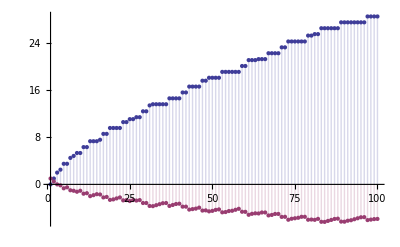

```mathematica
Clear[Ds]
binomial[z_,k_]:=binomial[z,k]=Product[z-j,{j,0,k-1}]/k!
Ds[n_,0,s_,a_]:=UnitStep[n-1]
Ds[n_,1,s_,a_]:=Ds[n,1,s,a]=HarmonicNumber[Floor[n],s]-HarmonicNumber[a,s]
Ds[n_,2,s_,a_]:=Ds[n,2,s,a]=Sum[(m^(-2s))+2(m^-s) (Ds[Floor[n/m],1,s,m]),{m,a+1,Floor[n^(1/2)]}]
Ds[n_,k_,s_,a_]:=Ds[n,k,s,a]=Sum[(m^(-s k))+k(m^(-s(k-1))) Ds[Floor[n/(m^(k-1))],1,s,m]+Sum[binomial[k,j] (m^-s)^j Ds[Floor[n/(m^j)],k-j,s,m],{j,1,k-2}],{m,a+1,Floor[n^(1/k)]}]

Dnsz[n_,s_,1]:=Expand@Sum[binomial[1,k]Ds[n,k,s,1],{k,0,1}]
Dnsz[n_,s_,z_]:=Expand@Sum[binomial[z,k]Ds[n,k,s,1],{k,0,Log2@n}]

lgm[n_]:=Sum[ BernoulliB[ k]/k! D[Dnsz[n,0,z],{z,k}]/.z->0,{k,0,Log2@n}]

DiscretePlot[ {(D[Dnsz[n,0,z],z]/.z->0),lgm[n]},{n,1,100}]
```

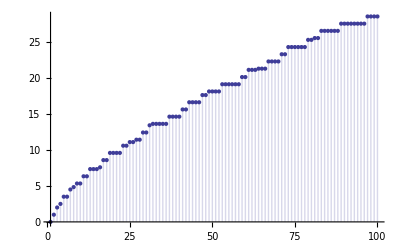

```mathematica
DiscretePlot[ Sum[ lgm[n/j],{j,2,n}],{n,1,100}]
```

```mathematica
Series[Log[x]/(x-1),{x,1,20}]
```

1-(x-1)/2+1/3 (x-1)^2-1/4 (x-1)^3+1/5 (x-1)^4-1/6 (x-1)^5+1/7 (x-1)^6-1/8 (x-1)^7+1/9 (x-1)^8-1/10 (x-1)^9+1/11 (x-1)^10-1/12 (x-1)^11+1/13 (x-1)^12-1/14 (x-1)^13+1/15 (x-1)^14-1/16 (x-1)^15+1/17 (x-1)^16-1/18 (x-1)^17+1/19 (x-1)^18-1/20 (x-1)^19+1/21 (x-1)^20+O[x-1]^21

```mathematica
Series[1/x,{x,1,20}]
```

1-(x-1)+(x-1)^2-(x-1)^3+(x-1)^4-(x-1)^5+(x-1)^6-(x-1)^7+(x-1)^8-(x-1)^9+(x-1)^10-(x-1)^11+(x-1)^12-(x-1)^13+(x-1)^14-(x-1)^15+(x-1)^16-(x-1)^17+(x-1)^18-(x-1)^19+(x-1)^20+O[x-1]^21

```mathematica
Series[(x-1)/Log[x],{x,1,20}]
```

1+(x-1)/2-1/12 (x-1)^2+1/24 (x-1)^3-19/720 (x-1)^4+3/160 (x-1)^5-(863 (x-1)^6)/60480+(275 (x-1)^7)/24192-(33953 (x-1)^8)/3628800+(8183 (x-1)^9)/1036800-(3250433 (x-1)^10)/479001600+(4671 (x-1)^11)/788480-(13695779093 (x-1)^12)/2615348736000+(2224234463 (x-1)^13)/475517952000-(132282840127 (x-1)^14)/31384184832000+(2639651053 (x-1)^15)/689762304000-(111956703448001 (x-1)^16)/32011868528640000+(50188465 (x-1)^17)/15613165568-(2334028946344463 (x-1)^18)/786014494949376000+(301124035185049 (x-1)^19)/109285437800448000-(12365722323469980029 (x-1)^20)/4817145976189747200000+O[x-1]^21

```mathematica
Series[(x-1)/Log[x],{x,1,20}]
```

1+(x-1)/2-1/12 (x-1)^2+1/24 (x-1)^3-19/720 (x-1)^4+3/160 (x-1)^5-(863 (x-1)^6)/60480+(275 (x-1)^7)/24192-(33953 (x-1)^8)/3628800+(8183 (x-1)^9)/1036800-(3250433 (x-1)^10)/479001600+(4671 (x-1)^11)/788480-(13695779093 (x-1)^12)/2615348736000+(2224234463 (x-1)^13)/475517952000-(132282840127 (x-1)^14)/31384184832000+(2639651053 (x-1)^15)/689762304000-(111956703448001 (x-1)^16)/32011868528640000+(50188465 (x-1)^17)/15613165568-(2334028946344463 (x-1)^18)/786014494949376000+(301124035185049 (x-1)^19)/109285437800448000-(12365722323469980029 (x-1)^20)/4817145976189747200000+O[x-1]^21

```mathematica
Series[Log[x]/(x-1)^2,{x,1,20}]
```

1/(x-1)-1/2+(x-1)/3-1/4 (x-1)^2+1/5 (x-1)^3-1/6 (x-1)^4+1/7 (x-1)^5-1/8 (x-1)^6+1/9 (x-1)^7-1/10 (x-1)^8+1/11 (x-1)^9-1/12 (x-1)^10+1/13 (x-1)^11-1/14 (x-1)^12+1/15 (x-1)^13-1/16 (x-1)^14+1/17 (x-1)^15-1/18 (x-1)^16+1/19 (x-1)^17-1/20 (x-1)^18+1/21 (x-1)^19-1/22 (x-1)^20+O[x-1]^21

```mathematica
Series[1/(x-1),{x,2,20}]
```

1-(x-2)+(x-2)^2-(x-2)^3+(x-2)^4-(x-2)^5+(x-2)^6-(x-2)^7+(x-2)^8-(x-2)^9+(x-2)^10-(x-2)^11+(x-2)^12-(x-2)^13+(x-2)^14-(x-2)^15+(x-2)^16-(x-2)^17+(x-2)^18-(x-2)^19+(x-2)^20+O[x-2]^21

```mathematica
Clear[dm]
dm[n_,k_] := dm[n,k]=Sum[ dm[Floor[n/j],k-1],{j,2,n}]-dm[n,k-1]
dm[n_,0] := UnitStep[n-1]
```

```mathematica
Table[ dm[100,k],{k,0,20}]
```

{1,98,86,-229,191,35,-367,671,-791,572,124,-1409,3367,-6059,9535,-13853,19105,-25450,33154,-42637,54527}

```mathematica
Clear[d2]
d2[n_,k_] := d2[n,k]=Sum[ d2[Floor[n/j],k-1],{j,2,n}]
d2[n_,0] := UnitStep[n-1]
pk[n_,j_]:=Sum[ (-1)^(k+j+1)/(k+j)d2[n,k],{k,0,Log2@n}]
pks[n_,j_]:=Sum[ (-1)^(k+1)/(k)d2[n,k+j],{k,1,Log2@n}]
```

```mathematica
DiscretePlot[Sum[ pk[n/j,1],{j,2,n}] ,{n,1,100}]
```

-Graphics-

```mathematica
Series[Log[x]/x,{x,1,20}]
```

(x-1)-3/2 (x-1)^2+11/6 (x-1)^3-25/12 (x-1)^4+137/60 (x-1)^5-49/20 (x-1)^6+363/140 (x-1)^7-761/280 (x-1)^8+(7129 (x-1)^9)/2520-(7381 (x-1)^10)/2520+(83711 (x-1)^11)/27720-(86021 (x-1)^12)/27720+(1145993 (x-1)^13)/360360-(1171733 (x-1)^14)/360360+(1195757 (x-1)^15)/360360-(2436559 (x-1)^16)/720720+(42142223 (x-1)^17)/12252240-(14274301 (x-1)^18)/4084080+(275295799 (x-1)^19)/77597520-(55835135 (x-1)^20)/15519504+O[x-1]^21

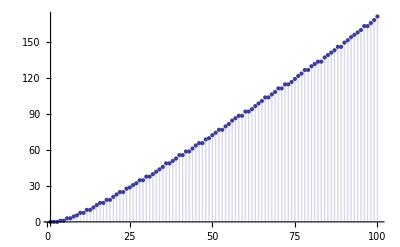

```mathematica
DiscretePlot[ pks[n,1] ,{n,1,100}]
```

```mathematica
Sum[ Sum[(D[Log[x]/x,{x,k}]/k!/.x->1)d2[100/j,k],{j,1,100}],{k,1,Log2@100}]
```

428/15

```mathematica
Sum[ (D[Log[x]/x,{x,k}]/k!/.x->1)Sum[d2[100/j,k],{j,1,100}],{k,1,Log2@100}]
```

428/15

```mathematica
Sum[ (D[Log[x]/x,{x,k}]/k!/.x->1)(d2[100,k+1]+d2[100,k]),{k,1,Log2@100}]
```

428/15

```mathematica
Sum[ BernoulliB[k]/k! (Log[x])^k,{k,0,Infinity}]
```

Log[x]/(-1+x)

```mathematica
Series[Log[x] x,{x,1,20}]
```

(x-1)+1/2 (x-1)^2-1/6 (x-1)^3+1/12 (x-1)^4-1/20 (x-1)^5+1/30 (x-1)^6-1/42 (x-1)^7+1/56 (x-1)^8-1/72 (x-1)^9+1/90 (x-1)^10-1/110 (x-1)^11+1/132 (x-1)^12-1/156 (x-1)^13+1/182 (x-1)^14-1/210 (x-1)^15+1/240 (x-1)^16-1/272 (x-1)^17+1/306 (x-1)^18-1/342 (x-1)^19+1/380 (x-1)^20+O[x-1]^21

```mathematica
Sum[ (D[Log[x] x,{x,k}]/k!/.x->1)Sum[MoebiusMu[j]d2[100/j,k],{j,1,100}],{k,1,Log2@100}]
```

428/15

```mathematica
Series[Log[x] /Cos[x],{x,0,20}]
```

Log[x]+1/2 Log[x] x^2+5/24 Log[x] x^4+61/720 Log[x] x^6+(277 Log[x] x^8)/8064+(50521 Log[x] x^10)/3628800+(540553 Log[x] x^12)/95800320+(199360981 Log[x] x^14)/87178291200+(3878302429 Log[x] x^16)/4184557977600+(2404879675441 Log[x] x^18)/6402373705728000+(14814847529501 Log[x] x^20)/97316080327065600+O[x]^21

```mathematica
Sum[1/k! (Log[x])^k,{k,0,Infinity}]
```

x

```mathematica
Sum[ (Log[x])^k,{k,0,Infinity}]
```

1/(1-Log[x])

```mathematica
Sum[(-1)^k (Log[x])^k,{k,0,Infinity}]
```

1/(1+Log[x])

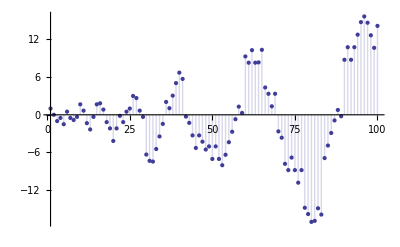

```mathematica
kap[n_]:= kap[n] = FullSimplify[MangoldtLambda[n]/Log[n]]
k2[n_,k_]:=k2[n,k]=Sum[ kap[j]k2[Floor[n/j],k-1],{j,2,n}]
k2[n_,0]:=UnitStep[n-1]

DiscretePlot[ Sum[ (-1)^k k2[n,k],{k,0,Log2@n}],{n,1,100}]
```

```mathematica
2(Sum[ BernoulliB[ k]/k! D[Dnsz[100,0,z],{z,k}]/.z->0,{k,2,Log2@100}]-lgm[100]+1)
```

428/15

```mathematica
lgmk[n_,t_]:=Sum[ BernoulliB[k]/k! (Log[x])^(k+t),{k,0,Infinity}]
```

```mathematica
lgmk[100,-1]
```

1/(-1+x)

```mathematica
Table[BernoulliB[k]/k!,{k,0,10}]
```

{1,-1/2,1/12,0,-1/720,0,1/30240,0,-1/1209600,0,1/47900160}

```mathematica
Series[(x-1)/Log[x],{x,1,20}]
```

1+(x-1)/2-1/12 (x-1)^2+1/24 (x-1)^3-19/720 (x-1)^4+3/160 (x-1)^5-(863 (x-1)^6)/60480+(275 (x-1)^7)/24192-(33953 (x-1)^8)/3628800+(8183 (x-1)^9)/1036800-(3250433 (x-1)^10)/479001600+(4671 (x-1)^11)/788480-(13695779093 (x-1)^12)/2615348736000+(2224234463 (x-1)^13)/475517952000-(132282840127 (x-1)^14)/31384184832000+(2639651053 (x-1)^15)/689762304000-(111956703448001 (x-1)^16)/32011868528640000+(50188465 (x-1)^17)/15613165568-(2334028946344463 (x-1)^18)/786014494949376000+(301124035185049 (x-1)^19)/109285437800448000-(12365722323469980029 (x-1)^20)/4817145976189747200000+O[x-1]^21

```mathematica
Sum[BernoulliB[k]/k! Log[x]^k,{k,0,Infinity}]
```

Log[x]/(-1+x)

```mathematica
Sum[BernoulliB[k]/k! Log[x]^(k+1),{k,0,Infinity}]
```

Log[x]^2/(-1+x)

```mathematica
Sum[BernoulliB[k]/k! Log[x]^(k-1),{k,0,Infinity}]
```

1/(-1+x)

```mathematica
Series[(x-1)/Log[x],{x,1,20}]
```

1+(x-1)/2-1/12 (x-1)^2+1/24 (x-1)^3-19/720 (x-1)^4+3/160 (x-1)^5-(863 (x-1)^6)/60480+(275 (x-1)^7)/24192-(33953 (x-1)^8)/3628800+(8183 (x-1)^9)/1036800-(3250433 (x-1)^10)/479001600+(4671 (x-1)^11)/788480-(13695779093 (x-1)^12)/2615348736000+(2224234463 (x-1)^13)/475517952000-(132282840127 (x-1)^14)/31384184832000+(2639651053 (x-1)^15)/689762304000-(111956703448001 (x-1)^16)/32011868528640000+(50188465 (x-1)^17)/15613165568-(2334028946344463 (x-1)^18)/786014494949376000+(301124035185049 (x-1)^19)/109285437800448000-(12365722323469980029 (x-1)^20)/4817145976189747200000+O[x-1]^21

```mathematica
Series[(x-1)^2/Log[x],{x,1,20}]
```

(x-1)+1/2 (x-1)^2-1/12 (x-1)^3+1/24 (x-1)^4-19/720 (x-1)^5+3/160 (x-1)^6-(863 (x-1)^7)/60480+(275 (x-1)^8)/24192-(33953 (x-1)^9)/3628800+(8183 (x-1)^10)/1036800-(3250433 (x-1)^11)/479001600+(4671 (x-1)^12)/788480-(13695779093 (x-1)^13)/2615348736000+(2224234463 (x-1)^14)/475517952000-(132282840127 (x-1)^15)/31384184832000+(2639651053 (x-1)^16)/689762304000-(111956703448001 (x-1)^17)/32011868528640000+(50188465 (x-1)^18)/15613165568-(2334028946344463 (x-1)^19)/786014494949376000+(301124035185049 (x-1)^20)/109285437800448000+O[x-1]^21

```mathematica
Series[(x-1)^3/Log[x],{x,1,20}]
```

(x-1)^2+1/2 (x-1)^3-1/12 (x-1)^4+1/24 (x-1)^5-19/720 (x-1)^6+3/160 (x-1)^7-(863 (x-1)^8)/60480+(275 (x-1)^9)/24192-(33953 (x-1)^10)/3628800+(8183 (x-1)^11)/1036800-(3250433 (x-1)^12)/479001600+(4671 (x-1)^13)/788480-(13695779093 (x-1)^14)/2615348736000+(2224234463 (x-1)^15)/475517952000-(132282840127 (x-1)^16)/31384184832000+(2639651053 (x-1)^17)/689762304000-(111956703448001 (x-1)^18)/32011868528640000+(50188465 (x-1)^19)/15613165568-(2334028946344463 (x-1)^20)/786014494949376000+O[x-1]^21

```mathematica
Series[1/Log[x],{x,1,20}]
```

1/(x-1)+1/2-(x-1)/12+1/24 (x-1)^2-19/720 (x-1)^3+3/160 (x-1)^4-(863 (x-1)^5)/60480+(275 (x-1)^6)/24192-(33953 (x-1)^7)/3628800+(8183 (x-1)^8)/1036800-(3250433 (x-1)^9)/479001600+(4671 (x-1)^10)/788480-(13695779093 (x-1)^11)/2615348736000+(2224234463 (x-1)^12)/475517952000-(132282840127 (x-1)^13)/31384184832000+(2639651053 (x-1)^14)/689762304000-(111956703448001 (x-1)^15)/32011868528640000+(50188465 (x-1)^16)/15613165568-(2334028946344463 (x-1)^17)/786014494949376000+(301124035185049 (x-1)^18)/109285437800448000-(12365722323469980029 (x-1)^19)/4817145976189747200000+(8519318716801273673 (x-1)^20)/3549475982455603200000+O[x-1]^21

```mathematica
LaplaceTransform[2t^2 - 7t + 1,t,s]
```

4/s^3-7/s^2+1/s

```mathematica
Expand@DZ[100,0,x]
```

1+(428 x)/15+(16289 x^2)/360+(331 x^3)/16+(611 x^4)/144+(67 x^5)/240+(7 x^6)/720

```mathematica
LaplaceTransform[1+(428 t)/15+(16289 t^2)/360+(331 t^3)/16+(611 t^4)/144+(67 t^5)/240+(7 t^6)/720,t,s]
```

7/s^7+67/(2 s^6)+611/(6 s^5)+993/(8 s^4)+16289/(180 s^3)+428/(15 s^2)+1/s

```mathematica
Expand@InverseLaplaceTransform[7/s^7+67/(2 s^6)+611/(6 s^5)+993/(8 s^4)+16289/(180 s^3)+428/(15 s^2)+1/s,s,t]
```

1+(428 t)/15+(16289 t^2)/360+(331 t^3)/16+(611 t^4)/144+(67 t^5)/240+(7 t^6)/720

```mathematica
Expand@DZ[100,0,s]
```

1+(428 s)/15+(16289 s^2)/360+(331 s^3)/16+(611 s^4)/144+(67 s^5)/240+(7 s^6)/720

```mathematica
Expand@InverseLaplaceTransform[1+(428 s)/15+(16289 s^2)/360+(331 s^3)/16+(611 s^4)/144+(67 s^5)/240+(7 s^6)/720,s,t]
```

DiracDelta[t]+(428 DiracDelta'[t])/15+(16289 DiracDelta''[t])/360+331/16 DiracDelta^(3)[t]+611/144 DiracDelta^(4)[t]+67/240 DiracDelta^(5)[t]+7/720 DiracDelta^(6)[t]

```mathematica
ff[s_]:=7/s^7+67/(2 s^6)+611/(6 s^5)+993/(8 s^4)+16289/(180 s^3)+428/(15 s^2)+1/s
```

```mathematica
D[1+(428 x)/15+(16289 x^2)/360+(331 x^3)/16+(611 x^4)/144+(67 x^5)/240+(7 x^6)/720,x]
```

428/15+(16289 x)/180+(993 x^2)/16+(611 x^3)/36+(67 x^4)/48+(7 x^5)/120

```mathematica
t100[x_]:=1+(428 x)/15+(16289 x^2)/360+(331 x^3)/16+(611 x^4)/144+(67 x^5)/240+(7 x^6)/720
t100a[x_]:=(1+(428 x)/15+(16289 x^2)/360+(331 x^3)/16+(611 x^4)/144+(67 x^5)/240+(7 x^6)/720)
```

```mathematica
Chop@N[Sum[DZ[100,0,E^(2 Pi I/100 n)],{n,1,100}]/100]
```

1.

```mathematica
kap[n_]:= kap[n] = FullSimplify[MangoldtLambda[n]/Log[n]]
k2[n_,k_]:=k2[n,k]=Sum[ kap[j]k2[Floor[n/j],k-1],{j,2,n}]
k2[n_,0]:=UnitStep[n-1]
```

```mathematica
Expand@D[DZ[100,0,z],z]
```

428/15+(16289 z)/180+(993 z^2)/16+(611 z^3)/36+(67 z^4)/48+(7 z^5)/120

```mathematica
1+Integrate[ 428/15+(16289 z)/180+(993 z^2)/16+(611 z^3)/36+(67 z^4)/48+(7 z^5)/120,{z,0,4}]
```

3575

```mathematica
Integrate[ 428/15,{z,0,3}]
```

428/5

```mathematica
m2[n_,k_] := m2[n,k]=Sum[ Abs[MoebiusMu[j]] m2[Floor[n/j],k-1],{j,2,n}]
m2[n_, 0] := UnitStep[n-1]
m1[n_, z_] := Sum[ bin[z,k]m2[n,k],{k,0,Log2@n}]
lm1[n_, k_] := D[m1[n,z],{z,k}]/.z->0
lmm[n_]:=Sum[ BernoulliB[ k]/k! Sum[ Abs[MoebiusMu[j]]lm1[n/j,k],{j,2,n}],{k,0,Log2@n}]
```

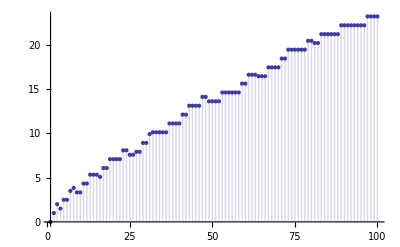

```mathematica
DiscretePlot[lmm[n],{n,1,100}]
```